```mathematica
Unprotect[npredictors];
SetDirectory[NotebookDirectory[]];
<<EQLab2`

(*measurements*)
ProbabilityPlus=0.5;
UserMeasure[]:=RandomReal[]//Which[#<ProbabilityPlus,1,True,-1]&(*simple yes or no answer with equal probability*)
(*forecasts*)
predictivepower2[xrandom_,meas_]:=Which[meas==1,1-xrandom^6,meas==-1,xrandom^6]
predictivepower1[xrandom_,meas_]:=Which[meas==1,1-xrandom^2,meas==-1,xrandom^2]
predictivepower0[xrandom_,meas_]:=Which[meas==1,1-xrandom,meas==-1,xrandom]
predictivepowerm1[xrandom_,meas_]:=Which[meas==1,xrandom^(7/6) ,meas==-1,1-xrandom^(7/6) ]
predictivepowerm2[xrandom_,meas_]:=Which[meas==1,xrandom^(3/2) ,meas==-1,1-xrandom^(3/2) ]

predictivepower[xrandom_,meas_,g_]:=Which[(*should correspond to p(ν,di) in Eq 17*)
g==2,predictivepower2[xrandom,meas],
g==1,predictivepower1[xrandom,meas],
g==0,predictivepower0[xrandom,meas],
g==-1,predictivepowerm1[xrandom,meas],
g==-2,predictivepowerm2[xrandom,meas]
]

INITIALbeliefinα={(*d_i in Eq 15. This array gets updated*)
2,  (*player A*)
1,  (*player B*)
0,   (*player C*)
-1,(*player D*)
-2    (*player E*)
};

beliefinα=INITIALbeliefinα;

affinity={(*'a' in Eq. 18*)
0,  (*player A*)
0,  (*player B*)
0,   (*player C*)
0,(*player D*)
0    (*player E*)
};

randomwalkprob={(*intended to play role of 'h' in random walk. *)
0.99,  (*player A*)
0.99,  (*player B*)
0.99,   (*player C*)
0.99,(*player D*)
0.99 (*player E*)
};

 PredictivePower=<|(*calls predictivepower functions with updated d_i*)
"A"->(predictivepower[#1,#2,beliefinα[[1]]]&),
"B"->(predictivepower[#1,#2,beliefinα[[2]]]&),
"C"->(predictivepower[#1,#2,beliefinα[[3]]]&),
"D"->(predictivepower[#1,#2,beliefinα[[4]]]&),
"E"->(predictivepower[#1,#2,beliefinα[[5]]]&)
|>;
 

npredictors=PredictivePower//Length; 


(*BadRewardDifference=400;*)
BeliefCurrent={};
BELIEF={};

(*this function updates beliefinα, d_i in draft, according to a random walk *)
RandomWalkv1[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,dorandomwalk={}},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;

dorandomwalk=Table[
TrueQ[Random[]<=randomwalkprob[[i]]],(*if ν<h, proceed with random walk*)
{i,1,beliefinα//Length}];

(*update d_i according to random walk*)
beliefinα=Table[
Which[
dorandomwalk[[i]]&&(Random[]>0.5),beliefinα[[i]]+1,
dorandomwalk[[i]],beliefinα[[i]]-1, 
True,beliefinα[[i]] 
],
{i,1,beliefinα//Length}
];

(*make sure that  -2 ≤ d_i ≤ 2, if not, force out of bounds values to wither +2 or -2*)
beliefinα=Table[
Which[
(beliefinα[[i]]<-2),beliefinα[[i]]=-2,
(beliefinα[[i]]>  2),beliefinα[[i]]=   2,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];

AppendTo[BeliefCurrent,beliefinα](*delete if using next step in update belief*)
]

RandomWalkv2[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,dorandomwalk={}},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;

dorandomwalk=Table[
TrueQ[Random[]<=randomwalkprob[[i]]],(*if ν<h, proceed with random walk*)
{i,1,beliefinα//Length}];

(*update d_i according to random walk*)
beliefinα=Table[
Which[
dorandomwalk[[i]]&&(Random[]>0.5),beliefinα[[i]]+1,
dorandomwalk[[i]],beliefinα[[i]]-1, 
True,beliefinα[[i]] 
],
{i,1,beliefinα//Length}
];

(*make sure that  -2 ≤ d_i ≤ 2, if not, set -3 -> -1 and 3 -> 1, to enforce walk*)
beliefinα=Table[
Which[
(beliefinα[[i]]==-3),beliefinα[[i]]=-1,
(beliefinα[[i]]==  3),beliefinα[[i]]=   1,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];

(*AppendTo[BeliefCurrent,beliefinα](*delete if using next step in update belief*)*)
]

RandomWalk=RandomWalkv2;


UpdateBelieveinαAffinity[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,changebelief={},beliefinαTEMP},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;

changebelief=Table[
TrueQ[
!(Random[]<Exp[- affinity[[i]](maxreward-rewards[[i]])])
]
,{i,1,beliefinα//Length}];


beliefinα=Table[
Which[
changebelief[[i]],beliefinα[[i]]+Sign[  beliefinα[[leadingexpert]]-beliefinα[[i]]  ],
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];
(*AppendTo[BeliefCurrent,beliefinα];*)

];

UpdateBelieveinα[]:=Module[
{},
RandomWalk[];
UpdateBelieveinαAffinity[];
AppendTo[BeliefCurrent,beliefinα];
]


PrintBelieveinα[]:=Module[
{names=PLOTLEGENDS[[1,1;;npredictors]],output},
output=Table[names[[i]]<>"->"<>ToString[beliefinα[[i]]]<>"\n",{i,1,npredictors}]//StringJoin;
Print[Style["------ Current belief in theory α ---------",Red,Large]];
Print[Style["after ",Bold,Large],Style[BeliefCurrent//Length,Bold,Large,Blue],Style[" questions.",Bold,Large]];
Print[Style[output,Blue,Large]]
]


UserPredict[exp_,newquestion_]:=Module[
{forecasts={}},
Which[
(exp//Length)>1,UpdateBelieveinα[];,
True,Nothing
];
forecasts=Table[RandomReal[{0.001,0.999}]//PredictivePower[i][#,newquestion[[2]]]&,{i,{"A","B","C","D","E"}}];
forecasts
]


(*resolutions*)

(*plays the role of 'b' in Eq 19 in draft *)
bias={
0,(*"A"*)
0,(*"B"*)
0,(*"C"*)
0,(*"D"*)
0    (*"E"*)
};

UserResolve[exp_,newquestion_]:=Module[
{objectiveSij,objectiveSjavg,resolutions,wj,i},
objectiveSij=ObjectiveSurprisal[newquestion];
objectiveSjavg=Mean[objectiveSij];
wj=newquestion[[2]];

resolutions=Table[
Which[
Random[]<Exp[-bias[[i]]*objectiveSij[[i]]/objectiveSjavg] , wj,
True,-wj
],
{i,1,newquestion[[1]]//Length}
]

]

(*condition to stop simulation*)
UserStop[]:=((beliefinα//DeleteDuplicates//Length)==1)&&Length[BeliefCurrent]>100;

(*load user function into EQLab*)
SetUserFunctions[]
nquestions=5000;

initsimulation[]:=Module[
{},
beliefinα=INITIALbeliefinα;
BeliefCurrent={};
AppendTo[BeliefCurrent,beliefinα]
]

outputsimulation[expi_,questioni_]:=Module[
{},
AppendTo[BELIEF,BeliefCurrent];
PrintBelieveinα[];
markerlist=marker2[White,#1,#2]&@@@(ColorData[97,"ColorList"]//Table[{#[[i]],50-i*7},{i,1,npredictors}]&);
plotbelief=BELIEF[[expi,questioni]]//Transpose//ListLinePlot[#,PlotMarkers->markerlist,PlotRange->{-2.5,2.5},ImageSize->{1000,500},LabelStyle->Directive[Bold, 16],AxesOrigin->{-(Length[#[[1]]]*0.05),-2.5},AxesLabel->{Style["j",Bold,Large],Style["d_i(j)",Bold,Large]},PlotLegends->PLOTLEGENDS,PlotStyle->Thick]&;
Print[plotbelief];

]

outputsimulation[]:=outputsimulation[-1,All]


Protect[npredictors];(*this simulation is written for 5 players only.*)
```

Example 1:  Affinity and random walk already in. Simulations stop after “agreement” is reached in the degree of belief of theory α, provided at least 100 questions have been asked. Simulation stops after ‘nquestions’ has been reached, even if no agreement happened.

{{2,1,0,-1,-2}}

------ Current belief in theory α ---------

after 121 questions.

expert A->0
expert B->0
expert C->0
expert D->0
expert E->0

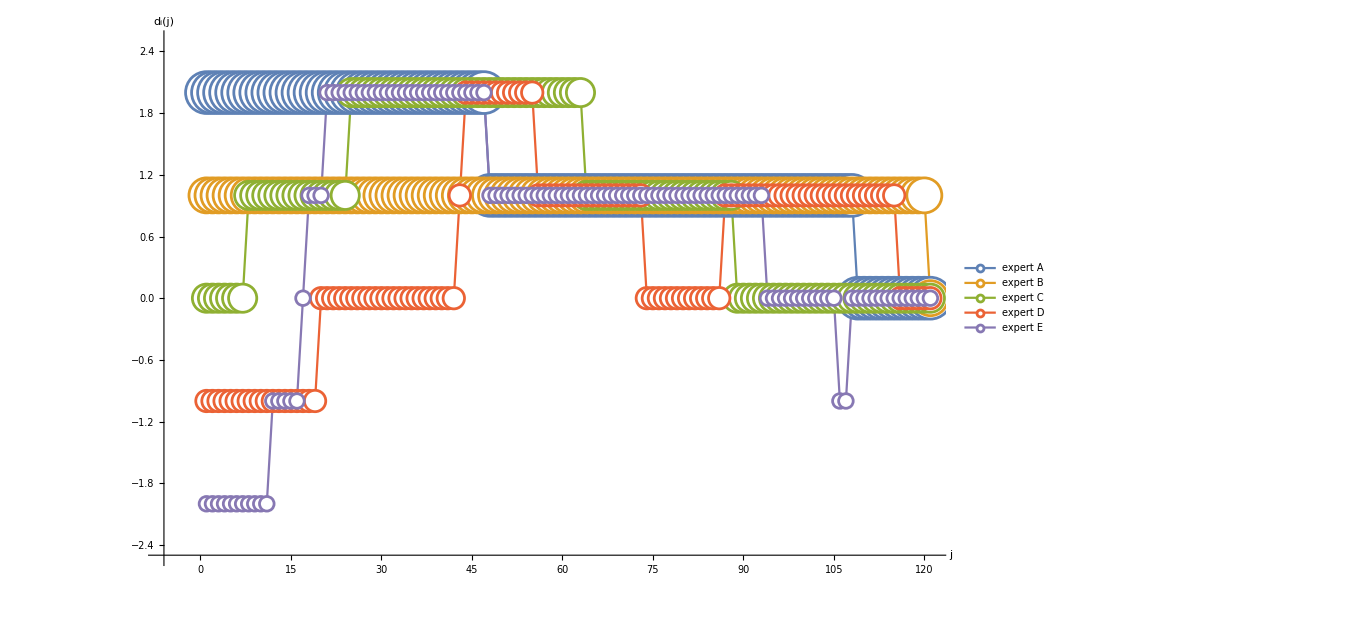

Diagram for last 20 questions:

------ Current belief in theory α ---------

after 121 questions.

expert A->0
expert B->0
expert C->0
expert D->0
expert E->0

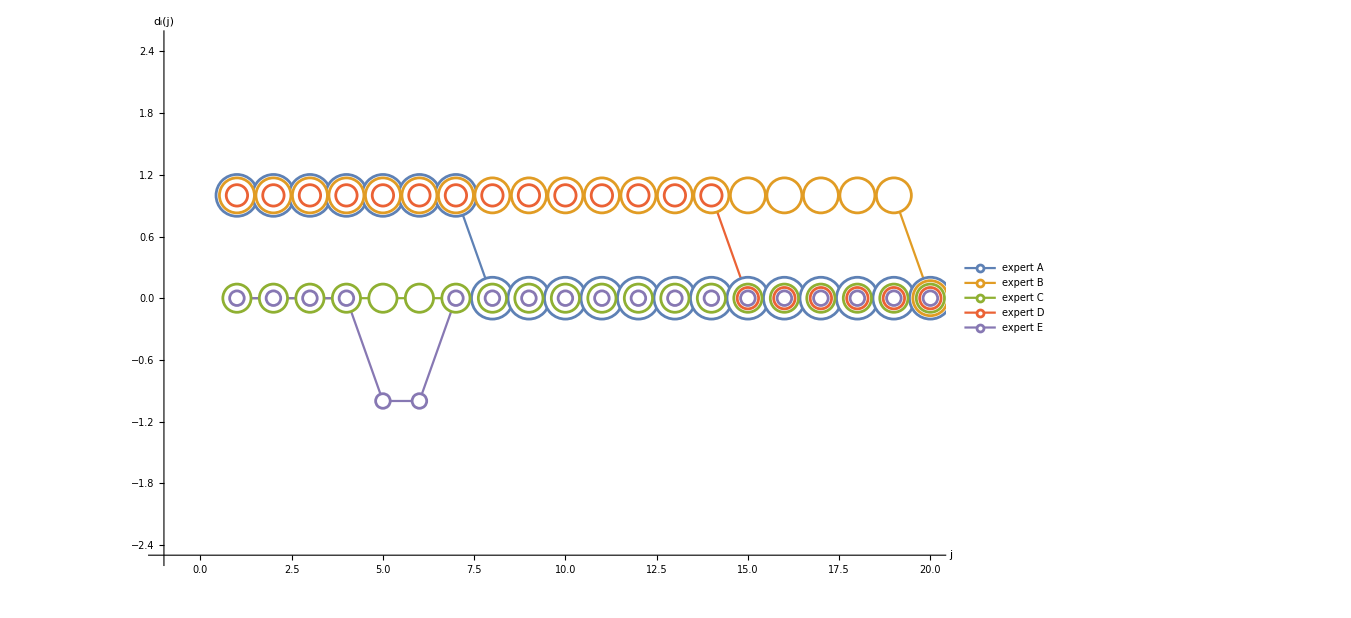

-Graphics-

-Graphics-

```mathematica
nquestions=2000;(*absolute max of questions asked*)
INITIALbeliefinα={
2,  (*player A*)
1,  (*player B*)
0,   (*player C*)
-1,(*player D*)
-2(*player E*)
};
randomwalkprob={(*intended to play role of 'h' in random walk. Note this is different from walk in the draft (discuss at meeting) *)
0.01,  (*player A*)
0.01,  (*player B*)
0.01,   (*player C*)
0.01,(*player D*)
0.01(*player E*)
};
affinity={(*'a' in Eq. 18*)
0.01,  (*player A*)
0.01,  (*player B*)
0.01,   (*player C*)
0.01,(*player D*)
0.01  (*player E*)
};
bias={
0.2,(*"A"*)
0.2,(*"B"*)
0.2,(*"C"*)
0.2,(*"D"*)
0.2    (*"E"*)
};

initsimulation[]
RunExperimentStop[]
outputsimulation[]
Print[Style["Diagram for last 20 questions:",Bold,Large]]
outputsimulation[-1,-20;;-1]
ShowPlots[-1,"rcumul"]
ShowPlots[-1,"savgj"]
```

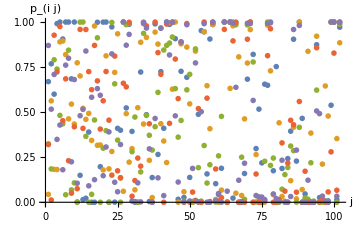
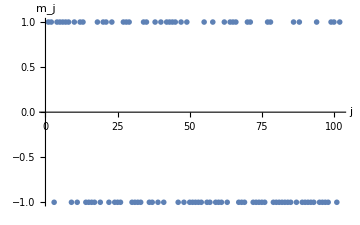
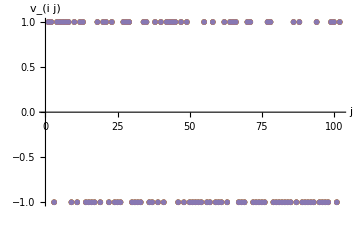
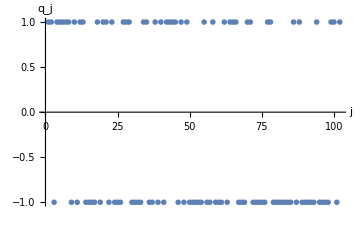
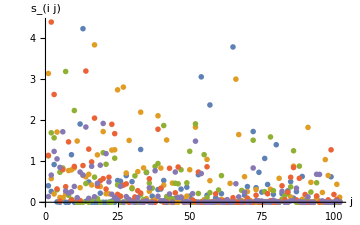
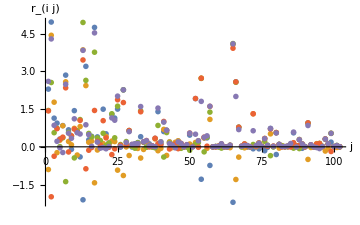
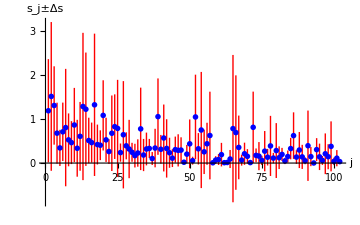
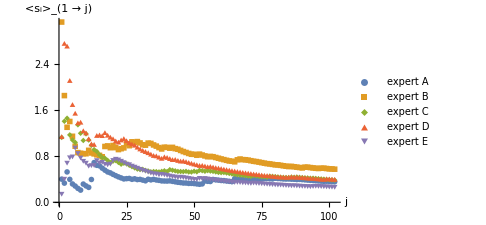
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
ShowPlots[-3]
```

```mathematica
Table[ShowPlots[i,"rcumul"],{i,1,EXPERIMENT//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

------ Current belief in theory α ---------

after 101 questions.

expert A->2
expert B->2
expert C->2
expert D->2
expert E->2

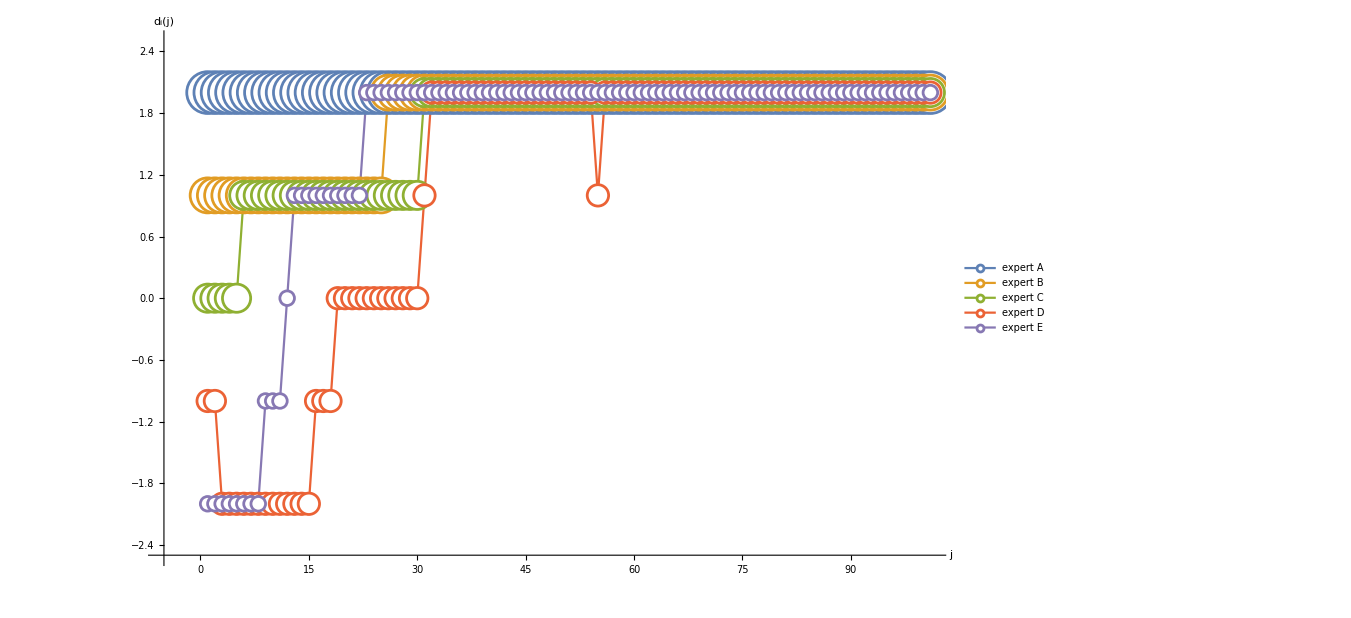

-Graphics-

```mathematica
outputsimulation[-3,All]
ShowPlots[-3,"rcumul"]
```